# Resposta de alguns elementos da matriz de Quadripolos para Linhas de Transmissão Aéreas

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\anton\Dropbox\[07] Codes\[EEE457]_codes\Mma

```mathematica
f1=Import["138CST1.csv"];
```

```mathematica
Dimensions[f1]
```

{29,9}

```mathematica
r=f1[[10,7]] ;
l=f1[[10,8]]/(2 π 60.);
c=f1[[10, 9]] 10^-6/(2 π 60.);
```

```mathematica
a[s_, ℓ_]:=With[{z= r + s l,y=s c},
 Cosh[Sqrt[z y] ℓ] ]
```

```mathematica
y1[s_, ℓ_]:=Module[{z= r + s l,y=s c, yc, γ},
γ=Sqrt[z y];
yc = Sqrt[y/z];
yc Coth[γ ℓ]
]
```

```mathematica
q={{123444., 456.},{456., 10^-7}};
q1={{123444., 456.},{456., 0.}};
```

```mathematica
Inverse[q]
```

{{-4.80917×10^-13,0.00219298},{0.00219298,-0.593663}}

```mathematica
Inverse[q1]
```

{{0.,0.00219298},{0.00219298,-0.593663}}

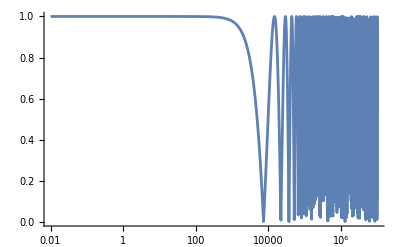

```mathematica
LogLinearPlot[Abs[a[I 2π f, 10]],{f, 0.01, 10^7}]
```

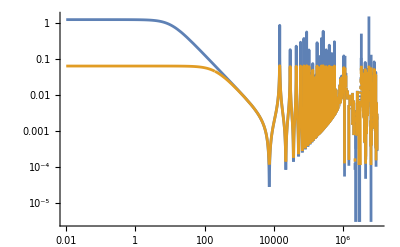

```mathematica
LogLogPlot[{Abs[y1[I 2π f, 10]],Abs[y1[1200+I 2π f, 10]]},{f, 0.01, 10^7}, PlotRange->All]
```

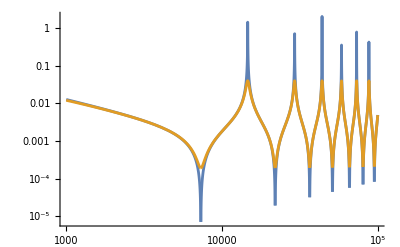

```mathematica
LogLogPlot[{Abs[y1[I 2π f, 10]],Abs[y1[2000+I 2π f, 10]]},{f, 10^3, 10^5}, PlotRange->All]
```